```mathematica
<<TopoTB`
```

#### Band

```mathematica
?VASPBand
```

```mathematica
path=SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
poscar=Import["POSCAR","Table"];
kpoints=Import["KPOINTS","Table"];
eigenval=Import["EIGENVAL","Table"];
efermi=-1.7400;
```

```mathematica
ds=VASPBand[poscar,kpoints,eigenval,efermi,1,1,"Band.dat"]
```

Dataset[<>]

```mathematica
?BandLabelsPlot
```

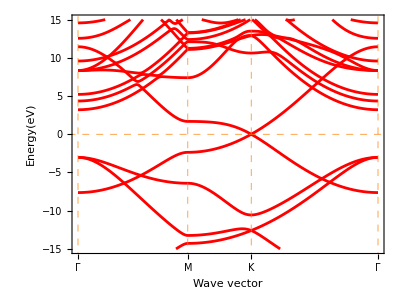

```mathematica
KK=Normal[ds[5]];
tband=Normal[ds[7]];
BandPlot[tband,KK,Red,0.005,3/4,{-15,15}]
```

```mathematica
KK=Normal[ds[5]];
tband=Normal[ds[7]];
BandLabelsPlot[tband,KK,Automatic,0.005,5/4,{-10,10}]
```

-Graphics-

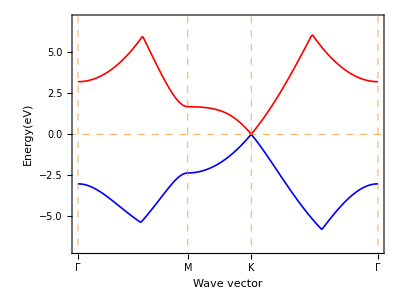

```mathematica
KK=Normal[ds[5]];
tband=Normal[ds[7]];
BandIndexPlot[{tband[[4]],tband[[5]]},KK,{Blue,Red},0.003,3/4,{-7,7}]
```

#### PBand

```mathematica
?VASPPBand
```

```mathematica
path=SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
poscar=Import["POSCAR","Table"];
kpoints=Import["KPOINTS","Table"];
procar=Import["PROCAR","Table"];
efermi=-1.7400;
```

```mathematica
(*ISPIN=1, UpOrDown=1 (any value is acceptable when ISPIN=1), SOC=1*)
ds=VASPPBand[poscar,kpoints,procar,efermi,1,1,1,{0},"PBand.dat"]
(*ds=VASPPBand[poscar,kpoints,procar,efermi,1,1,1,{1,2},"PBand.dat"]*)
```

Dataset[<>]

```mathematica
?PBandPlot
```

```mathematica
KK=Normal[ds[5]];
tpband=Normal[ds[7]];
Normal[ds[6]]
```

<|K-Path(1/Å)→{1},Energy(eV)→{2},s→{3},py→{4},pz→{5},px→{6},dxy→{7},dyz→{8},dz2→{9},dxz→{10},x2-y2→{11},tot→{12}|>

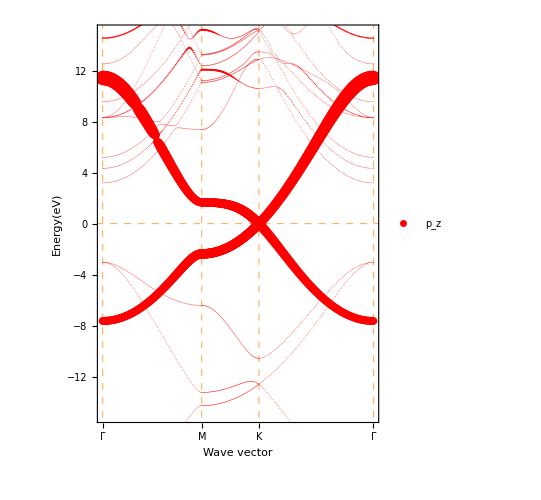

```mathematica
fig1=PBandPlot[tpband,KK,{5},Red,"p_z",30,5/4,{-15,15}]
```

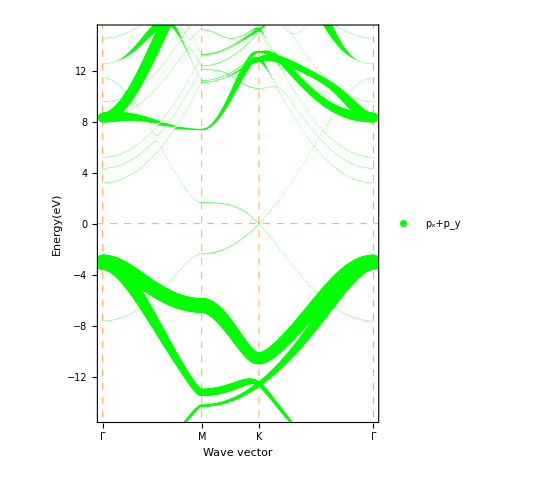

```mathematica
fig2=PBandPlot[tpband,KK,{4,6},Green,"p_x+p_y",30,5/4,{-15,15}]
```

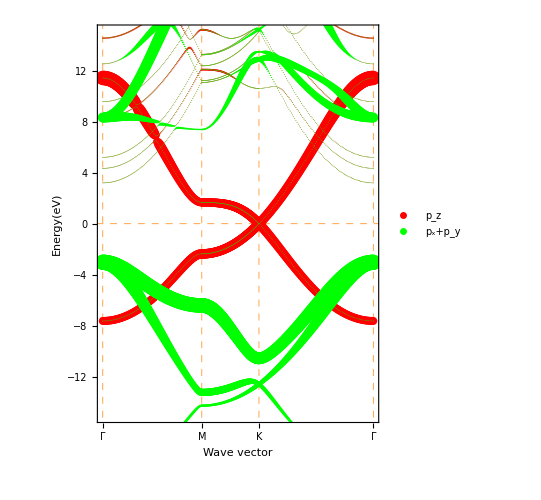

```mathematica
Show[fig1,fig2]
```